```mathematica
Clear["Global`*"]
```

# The three formulae for GW power and eccentricity, Peters and Mathews, Maggiore, and Amaro-Seoane et al.

## Notes

20171011  Cut out of the notebook GWExopEcc2.nb, weg.

## Directories, etc

```mathematica
(*myDir = "/scratch/gabella/Documents/astro/exop/";*)
(*thisDir = "/home/gabella/Documents/astro/exop/exoplanetsMath/";*)
thisDir = NotebookDirectory[];
csvDir = thisDir <>"dbases/";
pixDir = thisDir <>"pix/";
```

## Prelude

```mathematica
jj = BesselJ
bigA[n_,e_, asmaj_]:=asmaj^2/n(jj[n-2,n e]-jj[n+2,n e]-2 e jj[n-1,n e]+2 e jj[n+1,n e] )
bigB[n_,e_, asmaj_]:=(asmaj^2(1-e^2))/n(jj[n+2,n e]-jj[n-2,n e])
bigC[n_,e_, asmaj_]:=(asmaj^2 √(1-e^2))/n(jj[n+2,n e]+jj[n-2,n e]-e jj[n+1,n e]- e jj[n-1,n e] )
gg[n_,e_]:=n^6/(96 asmaj^4)(bigA[n,e,asmaj]^2+bigB[n,e,asmaj]^2+3 bigC[n,e,asmaj]^2-bigA[n,e,asmaj]*bigB[n,e,asmaj])/.asmaj->1  (* The asmaj's cancel out, so set equal to 1.  Same power of asmaj in bigA^2, bigB^2, bigC^2, and bigA*bigB as asmaj^4 *)
```

BesselJ

## The three formulae, Peters & Mathews eqn (20), Amaro-Seone et al. (4)-(6), and Maggiore (4.107-108). Check that they are the same. Similar looking and Bessel funtion identities might make them identical...one hopes.

Already have Maggiore’s formula above, gg[n_,e_,asmaj_].
Peters and Mathews, eqn 20.  The coefficient on eqn 19 is the same as in Maggiore.

```mathematica
ggPM[n_,e_]:= n^4/32( (jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n, n e]+2 e jj[n+1, n e]-jj[n+2, n e])^2+
(1-e^2)(jj[n-2,n e]-2 jj[n, n e]+jj[n+2, n e])^2 +4/(3 n^2)jj[n, n e]^2 )
```

Amaro-Seone et al.

```mathematica
bigAAS[n_,e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigBAS[n_,e_]:=jj[n-2,n e]-2 e jj[n-1,n e]+2/n jj[n,n e]+2 e jj[n+1,n e]-jj[n+2,n e]
ggAS[n_, e_]:=n^4/32(bigBAS[n,e]^2 + (1-e^2)bigAAS[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

```mathematica
Table[
ggPM[n,0.2]/ggPM[2,0],{n, 1, 6}
]
```

{0.00579633,0.814184,0.37536,0.0835568,0.0136303,0.00186696}

```mathematica
Table[
ggAS[n,0.2]/ggPM[2,0],{n, 1, 6}
]
```

{0.00579633,0.814184,0.37536,0.0835568,0.0136303,0.00186696}

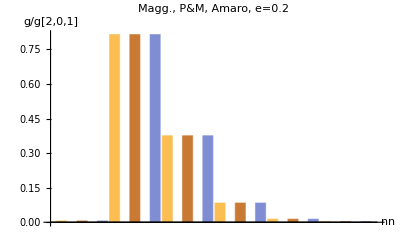

```mathematica
abar=BarChart[ Table[
{gg[n,0.2]/gg[2,0],ggPM[n,0.2]/ggPM[2,0],ggAS[n,0.2]/ggAS[2,0]},{n, 1, 6}
],
BarSpacing->1,PlotLabel->"Magg., P&M, Amaro, e=0.2",
AxesLabel->{"n", "g/g[2,0,1]"}
]
```

```mathematica
(*Export[pixDir<>"g_ecc0p2.png",abar,"PNG", ImageSize->{11,8.5}*72]*)
```

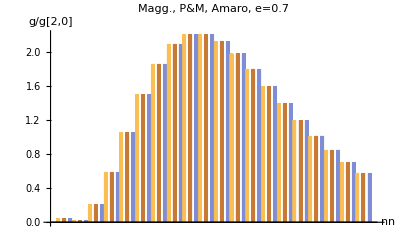

```mathematica
bbar=BarChart[ Table[
{gg[n,0.7]/gg[2,0],ggPM[n,0.7]/ggPM[2,0],ggAS[n,0.7]/ggAS[2,0]},{n, 1,20}
],
BarSpacing->1, PlotLabel->"Magg., P&M, Amaro, e=0.7",
AxesLabel->{"n", "g/g[2,0]"}]
```

```mathematica
(*Export[pixDir<>"g_ecc0p7.png",bbar,"PNG", ImageSize->{11,8.5}*72]*)
```

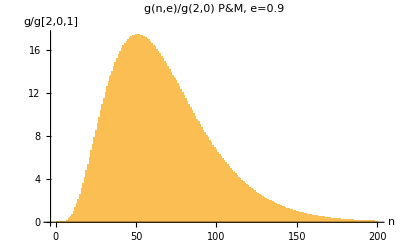

```mathematica
ecc=0.9;
cbar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,200}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = pixDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, cbar, "PNG", ImageSize->{11,8.5}*72]*)
```

Playing with strings.

```mathematica
pixDir<>"gPM_ecc0p"<>ToString[ Floor[ecc*10] ]<>".png" 
StringForm[pixDir<>"gPM_ecc0p``.png",Floor[ecc*10]]
```

/home/gabella/Documents/astro/exop/exoplanetsMath/pix/gPM_ecc0p9.png

/home/gabella/Documents/astro/exop/exoplanetsMath/pix/gPM_ecc0p9.png

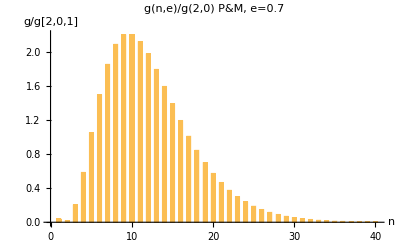

```mathematica
ecc=0.7;
dbar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,40}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = pixDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, dbar, "PNG", ImageSize->{11,8.5}*72]*)
```

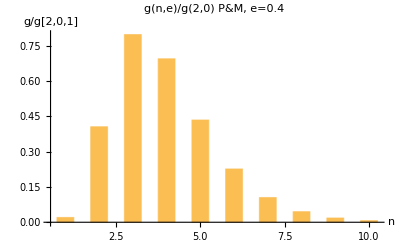

```mathematica
ecc=0.4;
ebar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,10}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = pixDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, ebar, "PNG", ImageSize->{11,8.5}*72]*)
```

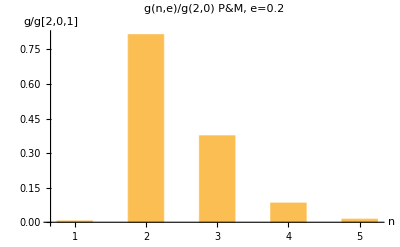

```mathematica
ecc=0.2;
fbar=
Show[
BarChart[ Table[
ggPM[n,ecc]/ggPM[2,0],{n, 1,5}
],
Axes->None,
Ticks->Automatic,
BarSpacing->1, PlotLabel->StringForm["g(n,e)/g(2,0) P&M, e=``",ecc],
AxesLabel->{"n", "g/g[2,0,1]"}
],
Axes->True,
Ticks->Automatic
]
fileString = pixDir<>"gPM_ecc0p"<>ToString[Floor[ecc*10]]<>".png" ;
(*Export[fileString, fbar, "PNG", ImageSize->{11,8.5}*72]*)
```

Make some plots for the paper here.  Below found from a Mathematica simplification of the full Bessel function mess...thank you Mathematica.

```mathematica
gred[n_,e_]:=n^2/(6 e^4)(
3 e^2 (-1+e^2) (-1+(-1+e^2) n^2) BesselJ[-1+n,e n]^2-3 e (-1+e^2) (-2+n (-2 (2+n)+e^2 (3+2 n))) BesselJ[-1+n,e n] BesselJ[n,e n]+(-3 e^6 n^2+6 (1+n)^2-3 e^2 (1+n) (2+5 n)+e^4 (1+3 n (3+4 n))) BesselJ[n,e n]^2   )
```

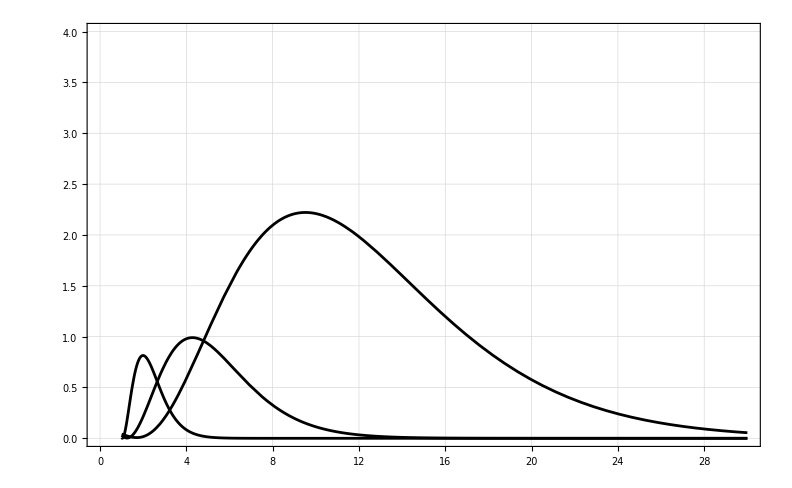
-Graphics-harmonic, nharmonic envelope, g(n,e)

```mathematica
If[True,   (* Just want a quick way to turn this off after I have the cool publication plot. *)
Module[{pubPlot,fontPts = 24, tScale=3, tickBig}, pubPlot = Labeled[
Plot[ {gg[n,0.2], gg[n,0.5], gg[n,0.7]},{n, 1, 30},
PlotRange->{{0,4}},
Frame->True,
GridLines->Automatic,
BaseStyle->Directive[AbsoluteThickness[1.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial" ],
GridLinesStyle->Directive[AbsoluteThickness[1.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial" ],
PlotStyle->Directive[AbsoluteThickness[2.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial"],
LabelStyle->Directive[AbsoluteThickness[1.0], RGBColor[0,0,0], fontPts, FontFamily->"Arial"],
AxesStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
FrameStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
TicksStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
FrameTicksStyle->Directive[AbsoluteThickness[1.0],fontPts,FontFamily->"Arial"],
LabelStyle->Directive[AbsoluteThickness[1.0],RGBColor[0,0,0],fontPts,FontFamily->"Arial"],
ImageSize->11*72
(*DisplayFunction->$DisplayFunction*)
],

{Style["harmonic, n", FontFamily->"Arial", FontSize->fontPts], 
Style["harmonic envelope, g(n,e)", FontFamily->"Arial", FontSize->fontPts]}, 
{Bottom, Left}, RotateLabel->True
];
(*tickBig=Map[MapAt[ tScale # & , #, 3]&, FrameTicks /. AbsoluteOptions[pubPlot, FrameTicks], {2}];*)
Export[pixDir<>"gofne.eps",pubPlot, "EPS" (*, ImageSize->{11,8.5}*72*)];
Show[pubPlot]
],
Null
]
(*Export[pixDir<>"g_ecc0p2.png",abar,"PNG", ImageSize->{11,8.5}*72]*)
```